```mathematica
Quit
```

XY 平面的 参数方程

```mathematica
x0[X_,Y_]:=X
```

```mathematica
y0[X_,Y_]:=Y
```

```mathematica
z0[X_,Y_]:=ArcTan[Y/X]
```

```mathematica
ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0,2 Pi},{Y,0,2 Pi}]
```

-Graphics3D-

VX VY是主方向

```mathematica
VX=FullSimplify[{Derivative[1,0][x0][X,Y],Derivative[1,0][y0][X,Y],Derivative[1,0][z0][X,Y]}]
```

{1,0,-Y/(X^2+Y^2)}

```mathematica
VY=FullSimplify[{Derivative[0,1][x0][X,Y],Derivative[0,1][y0][X,Y],Derivative[0,1][z0][X,Y]}]
```

{0,1,X/(X^2+Y^2)}

一些不变量

```mathematica
E0[X_,Y_]=FullSimplify[VX.VX]
```

1+Y^2/((X^2+Y^2)^2)

```mathematica
G0[X_,Y_]=FullSimplify[VY.VY]
```

1+X^2/((X^2+Y^2)^2)

面上任一点的两个切向量正交

```mathematica
F0[X_,Y_]=FullSimplify[VX.VY]
```

-(X Y)/((X^2+Y^2)^2)

VN 是面的法向

```mathematica
VN=FullSimplify[Cross[VX,VY]]
```

{Y/(X^2+Y^2),-X/(X^2+Y^2),1}

单位化

```mathematica
NVN=FullSimplify[VN/(Sqrt[VN.VN])]
```

{Y/((X^2+Y^2) √(1+1/(X^2+Y^2))),-X/((X^2+Y^2) √(1+1/(X^2+Y^2))),1/(√(1+1/(X^2+Y^2)))}

主方向的二阶导

```mathematica
VXX=FullSimplify[{Derivative[2,0][x0][X,Y],Derivative[2,0][y0][X,Y],Derivative[2,0][z0][X,Y]}]
```

{0,0,(2 X Y)/((X^2+Y^2)^2)}

```mathematica
VXY=FullSimplify[{Derivative[1,1][x0][X,Y],Derivative[1,1][y0][X,Y],Derivative[1,1][z0][X,Y]}]
```

{0,0,(-X^2+Y^2)/((X^2+Y^2)^2)}

```mathematica
VYY=FullSimplify[{Derivative[0,2][x0][X,Y],Derivative[0,2][y0][X,Y],Derivative[0,2][z0][X,Y]}]
```

{0,0,-(2 X Y)/((X^2+Y^2)^2)}

一些不变量

```mathematica
L0[X_,Y_]=FullSimplify[VXX.NVN]
```

(2 X Y)/((X^2+Y^2)^2 √(1+1/(X^2+Y^2)))

```mathematica
N0[X_,Y_]=FullSimplify[VYY.NVN]
```

-(2 X Y)/((X^2+Y^2)^2 √(1+1/(X^2+Y^2)))

```mathematica
M0[X_,Y_]=FullSimplify[VXY.NVN]
```

(-X^2+Y^2)/((X^2+Y^2)^2 √(1+1/(X^2+Y^2)))

执行坐标变换之后

```mathematica
Quit
```

```mathematica
(*U[X_,Y_]:=X (1+√(1+1/(X^2+Y^2)))*)
```

```mathematica
(*V[X_,Y_]:=Y (1+√(1+1/(X^2+Y^2)))*)
```

```mathematica
X[U_,V_]=1/2 U (1-1/(U^2+V^2));
Y[U_,V_]=1/2 V(1-1/(U^2+V^2));
```

```mathematica
x0[X_,Y_]:=X[U,V]
y0[X_,Y_]:=Y[U,V]
z0[X_,Y_]:=ArcTan[Y[U,V]/X[U,V]]
```

```mathematica
Evaluate[{x0[X,Y],y0[X,Y],z0[X,Y]}]//Simplify;
{x0[U_,V_],y0[U_,V_],z0[U_,V_]}=%
```

{1/2 U (1-1/(U^2+V^2)),1/2 V (1-1/(U^2+V^2)),ArcTan[V/U]}

```mathematica
{UMin,UMax}={0.1,1.1};
{VMin,VMax}={0.1,1.1};
```

```mathematica
{1/2 U (1-1/(U^2+V^2)),1/2 V (1-1/(U^2+V^2)),ArcTan[V/U]}/.{U->(a  U+b),V->(a  V+b)}//Simplify;
{x0[U_,V_],y0[U_,V_],z0[U_,V_]}=%
Manipulate[ParametricPlot3D[{%,{U,V,0}}, {U,0.4,1.4}, {V,0.4,1.4},PlotRange->All,PlotStyle->LightBlue],{{a,1},-10,10},{{b,0},-1,1}]
```

{1/2 U (1-1/(U^2+V^2)),1/2 V (1-1/(U^2+V^2)),ArcTan[V/U]}

```mathematica
{1/2 U (1-1/(U^2+V^2)),1/2 V (1-1/(U^2+V^2)),ArcTan[V/U]}/.{U->(a  U+b),V->(a  V+b)}//Simplify;
{x0[U_,V_],y0[U_,V_],z0[U_,V_]}=%
Manipulate[ParametricPlot3D[{%,{U,V,0}}, {U,0.1,1.1}, {V,0.1,1.1},PlotRange->All,PlotStyle->LightBlue],{{a,1},-10,10},{{b,0},-1,1}]
```

{1/2 (b+a U) (1-1/((b+a U)^2+(b+a V)^2)),1/2 (b+a V) (1-1/((b+a U)^2+(b+a V)^2)),ArcTan[(b+a V)/(b+a U)]}

```mathematica
a=1;
b=0;
```

重新计算 EFG LMN

VX VY是主方向

```mathematica
VX=FullSimplify[{Derivative[1,0][x0][U,V],Derivative[1,0][y0][U,V],Derivative[1,0][z0][U,V]}]
```

{1/2 (1+((U-V) (U+V))/((U^2+V^2)^2)),(U V)/((U^2+V^2)^2),-V/(U^2+V^2)}

```mathematica
VY=FullSimplify[{Derivative[0,1][x0][U,V],Derivative[0,1][y0][U,V],Derivative[0,1][z0][U,V]}]
```

{(U V)/((U^2+V^2)^2),1/2 (1+(-U^2+V^2)/((U^2+V^2)^2)),U/(U^2+V^2)}

一些不变量

```mathematica
E0[U_,V_]=FullSimplify[VX.VX]
```

((1+U^2+V^2)^2)/(4 (U^2+V^2)^2)

```mathematica
G0[U_,V_]=FullSimplify[VY.VY]
```

((1+U^2+V^2)^2)/(4 (U^2+V^2)^2)

面上任一点的两个切向量正交

```mathematica
F0[U_,V_]=FullSimplify[VX.VY]
```

0

VN 是面的法向

```mathematica
VN=FullSimplify[Cross[VX,VY]]
```

{(V (1+U^2+V^2))/(2 (U^2+V^2)^2),-(U (1+U^2+V^2))/(2 (U^2+V^2)^2),1/4-1/(4 (U^2+V^2)^2)}

单位化

```mathematica
NVN=FullSimplify[VN/(Sqrt[VN.VN])]
```

{(2 V (1+U^2+V^2))/((U^2+V^2)^2 √(((1+U^2+V^2)^4)/((U^2+V^2)^4))),-(2 U (1+U^2+V^2))/((U^2+V^2)^2 √(((1+U^2+V^2)^4)/((U^2+V^2)^4))),(-1+(U^2+V^2)^2)/((U^2+V^2)^2 √(((1+U^2+V^2)^4)/((U^2+V^2)^4)))}

主方向的二阶导

```mathematica
VXX=FullSimplify[{Derivative[2,0][x0][U,V],Derivative[2,0][y0][U,V],Derivative[2,0][z0][U,V]}]
```

{(-U^3+3 U V^2)/((U^2+V^2)^3),(V (-3 U^2+V^2))/((U^2+V^2)^3),(2 U V)/((U^2+V^2)^2)}

```mathematica
VXY=FullSimplify[{Derivative[1,1][x0][U,V],Derivative[1,1][y0][U,V],Derivative[1,1][z0][U,V]}]
```

{(V (-3 U^2+V^2))/((U^2+V^2)^3),(U (U^2-3 V^2))/((U^2+V^2)^3),(-U^2+V^2)/((U^2+V^2)^2)}

```mathematica
VYY=FullSimplify[{Derivative[0,2][x0][U,V],Derivative[0,2][y0][U,V],Derivative[0,2][z0][U,V]}]
```

{(U (U^2-3 V^2))/((U^2+V^2)^3),(3 U^2 V-V^3)/((U^2+V^2)^3),-(2 U V)/((U^2+V^2)^2)}

一些不变量

```mathematica
L0[U_,V_]=FullSimplify[VXX.NVN]
```

(2 U V √(((1+U^2+V^2)^4)/((U^2+V^2)^4)))/((1+U^2+V^2)^2)

```mathematica
N0[U_,V_]=FullSimplify[VYY.NVN]
```

-(2 U V √(((1+U^2+V^2)^4)/((U^2+V^2)^4)))/((1+U^2+V^2)^2)

```mathematica
M0[U_,V_]=FullSimplify[VXY.NVN]
```

((-U^2+V^2) √(((1+U^2+V^2)^4)/((U^2+V^2)^4)))/((1+U^2+V^2)^2)

计算生长函数
-Graphics-

```mathematica
λ=Simplify[√E0[U,V],U>0&&V>0]
```

(1+U^2+V^2)/(2 (U^2+V^2))

```mathematica
λ10=λ
λ20=λ
```

(1+U^2+V^2)/(2 (U^2+V^2))

(1+U^2+V^2)/(2 (U^2+V^2))

```mathematica
λ11=Simplify[(-L0[U,V])/λ,U>0&&V>0]
```

-(4 U V)/((U^2+V^2) (1+U^2+V^2))

```mathematica
λ12=Simplify[(-N0[U,V])/λ,U>0&&V>0]
```

(4 U V)/((U^2+V^2) (1+U^2+V^2))

```mathematica
λs=Simplify[(-M0[U,V])/λ,U>0&&V>0]
```

(2 (U^2-V^2))/((U^2+V^2) (1+U^2+V^2))

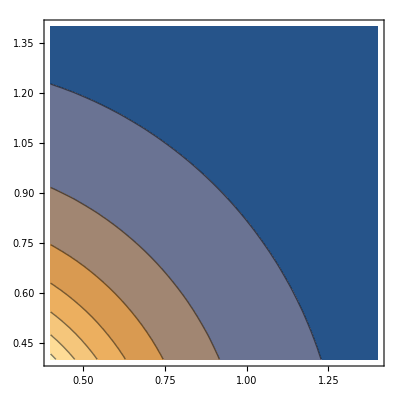

```mathematica
ContourPlot[λ10,{U,0.4,1.4},{V,0.4,1.4},PlotRange->All]
```

```mathematica
{x0[U,V],y0[U,V],z0[U,V]}//FullSimplify
```

{1/2 U (1-1/(U^2+V^2)),1/2 V (1-1/(U^2+V^2)),ArcTan[V/U]}

可以观察一下参考构型与当前构型各点间的对应关系

```mathematica
ParametricPlot3D[{x0[U,V],y0[U,V],z0[U,V]}, {U,UMin,UMax}, {V,VMin,VMax},PlotRange->All,PlotStyle->LightBlue];
ParametricPlot3D[{U,V,0}, {U,UMin,UMax}, {V,VMin,VMax},PlotRange->All,PlotStyle->Green];
RefCur=Show[%%,%];
```

```mathematica
Manipulate[Show[RefCur,ListPointPlot3D[Evaluate[{{x0[U,V],y0[U,V],z0[U,V]},{U,V,0}}/.{U-> a,V-> b}],PlotStyle->PointSize[Large]]],{a,UMin,UMax},{b,VMin,VMax}]
```

Show::gcomb: Could not combine the graphics objects in Show[RefCur,].

UV 的参数范围不能太靠近0，会出现无穷值，将其调整为 [0.1,1.1] ×[0.1,1.1]
接下来进入有限元验证